# Double Quadratic Spline Potential

## Boundary of the

```mathematica
LeftBoundary=-0.3221744234888432;
RightBoundary=0.1605538207017589;

Print["LBound: ",InputForm[LeftBoundary]]
Print["RBound: ",InputForm[RightBoundary]]
```

LBound: -0.3221744234888432

RBound: 0.1605538207017589

## Potential

PotL: 1.7724051019087494 + x*(6.1648873109869555 + 5.360771574771266*x)

PotC: 1. + x^2*(-7.395710880476022 + x*(6.600785187220504 + 30.72730601003735*x))

PotR: 1.0885716779019903 + (-1.5278198988098108 + 0.5360771574771266*x)*x

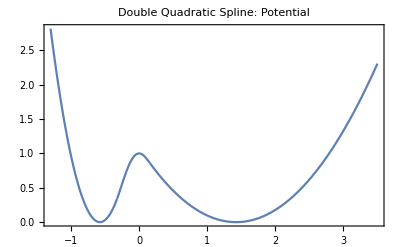

```mathematica
PotL=1.7724051019087494+x (6.1648873109869555+5.360771574771266 x);
PotC=0.9999999999999999+x^2 (-7.395710880476022+x (6.600785187220504+30.72730601003735 x));
PotR=1.0885716779019903+(-1.5278198988098108+0.5360771574771266 x) x;

Print["PotL: ",InputForm[HornerForm[PotL]]]
Print["PotC: ",InputForm[HornerForm[PotC]]]
Print["PotR: ",InputForm[HornerForm[PotR]]]

pltPotL=Plot[PotL,{x,-1.3,LeftBoundary}];
pltPotC=Plot[PotC,{x,LeftBoundary,RightBoundary}];
pltPotR=Plot[PotR,{x,RightBoundary,3.5}];

Show[pltPotL,pltPotC,pltPotR,PlotRange->All,Frame->True,PlotLabel->"Double Quadratic Spline: Potential"]
```

## Force

ForceL: -6.1648873109869555 - 10.721543149542532*x

ForceC: x*(14.791421760952044 + (-19.802355561661514 - 122.9092240401494*x)*x)

ForceR: 1.5278198988098108 - 1.0721543149542532*x

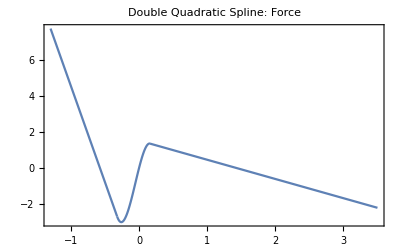

```mathematica
ForceL=-D[PotL,x];
ForceC=-D[PotC,x];
ForceR=-D[PotR,x];

Print["ForceL: ",InputForm[HornerForm[ForceL]]]
Print["ForceC: ",InputForm[HornerForm[ForceC]]]
Print["ForceR: ",InputForm[HornerForm[ForceR]]]

pltForceL=Plot[ForceL,{x,-1.3,LeftBoundary}];
pltForceC=Plot[ForceC,{x,LeftBoundary,RightBoundary}];
pltForceR=Plot[ForceR,{x,RightBoundary,3.5}];

Show[pltForceL,pltForceC,pltForceR,PlotRange->All,Frame->True,PlotLabel->"Double Quadratic Spline: Force"]
```

```mathematica
FindRoot[ForceL,{x,0}]
FindRoot[ForceR,{x,0}]
```

{x→-0.575}

{x→1.425}

## Hessian

HessianL: 10.721543149542532

HessianC: -14.791421760952044 + x*(39.60471112332303 + 368.7276721204482*x)

HessianR: 1.0721543149542532

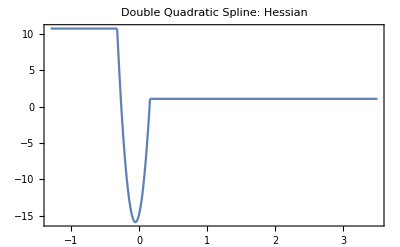

```mathematica
HessianL=D[PotL,{x,2}];
HessianC=D[PotC,{x,2}];
HessianR=D[PotR,{x,2}];

Print["HessianL: ",InputForm[HornerForm[HessianL]]]
Print["HessianC: ",InputForm[HornerForm[HessianC]]]
Print["HessianR: ",InputForm[HornerForm[HessianR]]]

pltHessianL=Plot[HessianL,{x,-1.3,LeftBoundary}];
pltHessianC=Plot[HessianC,{x,LeftBoundary,RightBoundary}];
pltHessianR=Plot[HessianR,{x,RightBoundary,3.5}];

Show[pltHessianL,pltHessianC,pltHessianR,PlotRange->All,Frame->True,PlotLabel->"Double Quadratic Spline: Hessian"]
```